```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["CrossSectionalPropertyMatrices`"];
```

import six-node triangular mesh method 1, import from *.inp file

```mathematica
meshfile=ReadABAQUSFile["T9.inp"];
gcoord=meshfile["nodes"][[;;,1;;2]];
gnum=meshfile["faceElements"]["Surface1"][[;;,2;;]];
```

import six-node triangular mesh method 2, import from *.xlsx file

```mathematica
{gcoord,gnum}=Import["C-shaped-mesh.xlsx"];
gnum=gnum[[;;,{1,3,5,2,4,6}]];
```

visualize the imported mesh data

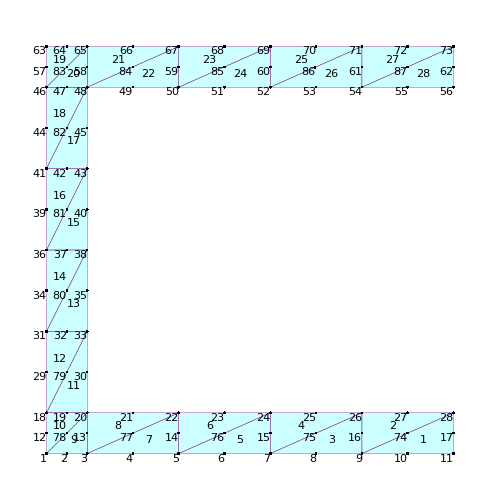

```mathematica
showMesh[gnum,gcoord,8,8,500]
```

```mathematica
E0=198.0*10^9;(* Elastic modulus *)
v=0.3; (* Poisson’s ratio *)
ρ=7850.0; (* mass density *)
gauss=gauss10;(* gauss quadrature rules data, with algebra precision 10 *)
{k,M,nu0}=mk0[E0,v,ρ,gauss,gcoord,gnum];
(*
k: cross-sectional stiffness matrix;
M: cross-sectional mass matrix;
nu0 : integration of the displacement shape function, which is used for generation of body force
*)
```

```mathematica
(* save the results to a MATLAB data file *)
Export["kmu.mat",{"k0"->k,"m0"->M,"nu0"->nu0},"Version"->Automatic];
```